```mathematica
(*Definizioni delle funzioni*)
LGP[j_,m_,θ_]:=N[Sqrt[(2 j+1)/(4 π) (j-m)!/(j+m)!]]*N[LegendreP[j,m,Cos[θ]]]

(*Funzione Clebsh-Gordan*)
CG[j_,m_,J_,M_]:=If[Abs[M-m]<=j&&Abs[M]<=J,N[ClebschGordan[{j,m},{j,M-m},{J,M}]],0]

(*Operatori di scala*)
Cplus[j_,m_]:=N[Sqrt[j (j+1)-m (m+1)]]
Cminus[j_,m_]:=N[Sqrt[j (j+1)-m (m-1)]]
```

```mathematica
(*Integrali*)
IntZZ[m_,n_]:=Module[{numerator,denominator,result},If[m==n,result=0,(*altrimenti,se m≠n*)numerator=I (-1+E^(I (-m+n) π/2))^3 (1+E^(I (-m+n) π/2));
denominator=m-n;
result=N[numerator/denominator]];
result//Chop]

IntXX[m_,n_]:=Module[{numerator,denominator,result},
If[m==n,result=1/2 E^(-(3/2) I m π) (1+E^(I m π)+E^(2 I m π)+E^(3 I m π)) π,
(*altrimenti,se m≠n*)result=-(1/(m-n)) I E^(-2 I m π) (E^((I m π)/2)-E^((I n π)/2)+E^(1/2 I (2 m+n) π)-E^(1/2 I (m+2 n) π)+E^(1/2 I (3 m+2 n) π)-E^(1/2 I (2 m+3 n) π)+E^(1/2 I (4 m+3 n) π)-E^(1/2 I (3 m+4 n) π));
result=N[result];
result//Chop] 
]

ClearAll[Integral]

(*Define a cache to store the results*)
integralCache=<||>;

(*Funzione per calcolare l'integrale I[m,n] con un sistema di caching*)
Integral[j_,m_,n_]:=Module[{key,result,integralPhi,integralTheta},

(*Generate a unique key for  and , independent on the order*)
key=Sort[{m,n}];

(*If the integral is already calculated, is recovered from the cache*)
If[KeyExistsQ[integralCache,key],

result=integralCache[key],

(*Otherwise it calculates the integral*)
(*Check if  and *)
If[Abs[m]>j||Abs[n]>j,Return[0]];

(*Calculate integralPhi and if it's ≠0, calculates also integralTheta*)
integralPhi=IntXX[m,n];

If[integralPhi==0,result=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];

result=Chop[integralPhi*integralTheta]];

(*Memorize the result in the cache*)
integralCache[key]=result;
];
result
]

(*Define a parallel version of the Integral function*)
ParallelIntegral[j_,m_,n_]:=Parallelize[Integral[j,m,n]]
```

```mathematica
(*Definizione della terza versione della funzione*)
ClearAll[TrAxComplete3];
TrAxComplete3[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term, timing},
If[J>2*j,Return[0]];
timing = AbsoluteTiming[
sumM=Sum[
cgm1=CG[j,m,J,M-m];
cgm2=CG[j,n,J,M-n];

If[cgm1!=0&&cgm2!=0,
term=Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1];

If[term!=0,cgm1*cgm2*term*(Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1]),
0],
0],
{m,-j,j},{n,-j,j},{M,-J,J}];

result=(1/4)*sumM;
Chop[result]];

Return[timing]
]
```

```mathematica
(*Lista dei valori di j e J*)jjValues={3,4,5};
JJValues=2*jjValues;

(*Inizializzazione della lista dei risultati*)
results={};

(*Loop attraverso i valori di jj e JJ*)
For[i=1,i<=Length[jjValues],i++,For[j=1,j<=Length[JJValues],j++,jValue=jjValues[[i]];
JValue=JJValues[[j]];
(*Esegui entrambe le versioni della funzione*)
{time1,result1}=TrAxComplete1[jValue,JValue];
{time2,result2}=TrAxComplete2[jValue,JValue];
{time3,result3}=TrAxComplete3[jValue,JValue];
(*Memorizza i risultati in una lista*)
AppendTo[results,{jValue,JValue,time1,time2,time3,result1,result2,result3}];]]

(*Stampa dei risultati*)
Print["j  | J  | Tempo versione 1 (s) | Tempo versione 2 (s) | Tempo versione 3 (s) | Risultato versione 1 | Risultato versione 2 | Risultato versione 3"];
resultsTable=TableForm[results,TableHeadings->{None,{"j","J","Tempo V1","Tempo V2","Tempo V3","Risultato V1","Risultato V2","Risultato V3"}}];

Print[resultsTable];
```

Parallelize::nopar1: Integral[3,-2,-3] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: Integral[3,-4,-3] cannot be parallelized; proceeding with sequential evaluation.

Parallelize::nopar1: Integral[3,-3,-2] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of Parallelize::nopar1 will be suppressed during this calculation.

Set::shape: Lists {time3,result3} and 0 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

j  | J  | Tempo versione 1 (s) | Tempo versione 2 (s) | Tempo versione 3 (s) | Risultato versione 1 | Risultato versione 2 | Risultato versione 3

j | J | Tempo V1 | Tempo V2 | Tempo V3 | Risultato V1 | Risultato V2 | Risultato V3
3 | 6 | 1.84423 | 1.78289 | 1.80898 | -4.71794 | -4.71794 | -4.71794
3 | 8 | 0 | 0 | 1.80898 | 0 | 0 | -4.71794
3 | 10 | 0 | 0 | 1.80898 | 0 | 0 | -4.71794
4 | 6 | 2.94829 | 2.87193 | 2.72831 | -6.83918 | -6.83918 | -6.83918
4 | 8 | 3.5448 | 3.58748 | 3.44921 | -2.27605 | -2.27605 | -2.27605
4 | 10 | 0 | 0 | 3.44921 | 0 | 0 | -2.27605
5 | 6 | 5.91057 | 5.96114 | 5.77667 | 7.65334 | 7.65334 | 7.65334
5 | 8 | 6.94044 | 7.06706 | 6.82253 | -15.7157 | -15.7157 | -15.7157
5 | 10 | 7.25407 | 7.43348 | 7.13328 | 0.54524 | 0.54524 | 0.54524

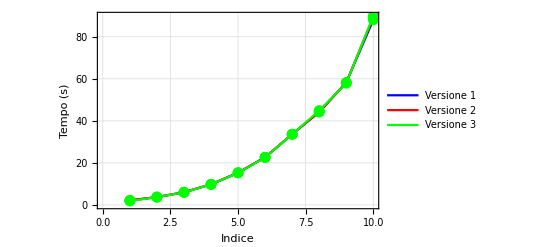

```mathematica
(*Estrai i dati dei tempi e degli indici dai risultati*)
timesV1=results[[All,3]]; (*Tempi versione 1*)
timesV2=results[[All,4]]; (*Tempi versione 2*)
timesV3=results[[All,5]]; (*Tempi versione 3*)

(*Crea un indice per ogni combinazione di j e J*)
indices=Range[Length[results]];

(*Crea il grafico dei tempi con le opzioni corrette*)
ListLinePlot[{timesV1,timesV2,timesV3},PlotStyle->{Blue,Red,Green},Mesh->All,MeshStyle->{Blue,Red,Green},GridLines->Automatic,Frame->True,FrameLabel->{"Indice","Tempo (s)","Tempi delle Versioni","Tempi di esecuzione delle tre versioni"},PlotLegends->{"Versione 1","Versione 2","Versione 3"}]
```